```mathematica
ClearAll["Global`*"];
```

```mathematica
t = 5;
```

```mathematica
u=0.1;
```

```mathematica
g=9.81;
```

```mathematica
ms = u*t;
Fc = u*v;
Fg = (m-ms)*g;
```

```mathematica
A = Solve[(m-ms)*a==Fc-Fg, a]
```

{{a→(-9.81 (-0.5+m)+0.1 v)/(-0.5+m)}}

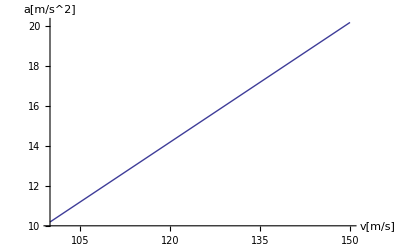

```mathematica
Plot[a/.A/.m -> 1, {v, 100, 150}, AxesLabel -> {"v[m/s]","a[m/s^2]"}]
```

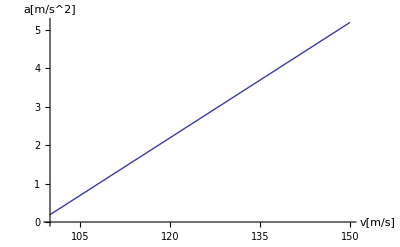

```mathematica
Plot[a/.A/.m -> 1.5, {v, 100, 150},  AxesLabel -> {"v[m/s]","a[m/s^2]"}]
```